```mathematica
(* ΟΡΘΟΓΩΝΙΟ ΦΡΕΑΡ ΔΥΝΑΜΙΚΟΥ *)
```

```mathematica
(* ΑΡΙΘΜΗΤΙΚΗ ΜΕΘΟΔΟΣ ΜΕ NDSolve, Part 1 *)
```

```mathematica
Clear["Global`*"];
```

```mathematica
(* ΟΡΙΣΜΟΣ ΣΤΑΘΕΡΩΝ, 1 ΓΙΑ ΑΤΟΜΙΚΑ ΚΑΙ 2 ΓΙΑ ΠΥΡΗΝΙΚΑ ΣΥΣΤΗΜΑΤΑ *)
```

```mathematica
ic=1;
Which[ ic==1, {c=26.247 , ctime=6.586*10^(-16)},
           ic==2, {c=0.0482, ctime=6.586*10^(-21)}];
```

```mathematica
(* ΟΡΙΣΜΟΣ ΠΑΡΑΜΕΤΡΩΝ ΤΟΥ ΔΥΝΑΜΙΚΟΥ ΚΑΙ ΠΙΝΑΚΩΝ ΓΙΑ ΤΙΣ ΕΝΕΡΓΕΙΣ ΚΑΙ ΤΑ ΣΧΗΜΑΤΑ *)
```

```mathematica
v0=300; L=0.2; 
eee=Table[Null,{20}]; 
fig=Table[Null,{20}];
```

```mathematica
(* ΟΡΙΣΜΟΣ ΔΥΝΑΜΙΚΟΥ *)
```

```mathematica
v[x_]:=Which[Abs[x]≤L,-v0 ,Abs[x] >L,0 ]
```

```mathematica
(* ΟΡΙΣΜΟΣ ΤΟΥ ΚΥΜΑΤΑΡΙΘΜΟΥ γ ΚΑΙ ΤΗΣ ΣΥΜΠΕΡΙΦΟΡΑΣ ΤΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ ΓΙΑ x<-L ΚΑΙ x>L *)
(* ΙΣΧΥΕΙ A1=B1 ΓΙΑ ΑΡΤΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ ΚΑΙ A1=1 ΚΑΙ B1=-1 ΓΙΑ ΤΙΣ ΠΕΡΙΤΤΕΣ *)
(* ΘΕΤΟΥΜΕ Α1 = Β3 = 1 *)
```

```mathematica
g[e_]:=Sqrt[-c*e];   
xmax[e_]=15.*Log[10]/g[e];
u1[e_,x_]:=Exp[ g[e]*x ]        
u3Even[e_,x_]:=Exp[- g[e]*x ] 
u3Odd[e_,x_]:=-Exp[- g[e]*x ]
```

```mathematica
(* ΟΡΙΣΜΟΣ ΣΥΝΟΛΙΚΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ ΓΙΑ ΑΡΤΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
wfEven[e_,uleft_,uright_]:=Which[x≤-L, u1[e,x],-L≤x≤0,uleft, 0≤x≤L,uright , x≥L,  u3Even[e,x]]
```

```mathematica
(* ΟΡΙΣΜΟΣ ΣΥΝΟΛΙΚΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ ΓΙΑ ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
wfOdd[e_,uleft_,uright_]:=Which[x≤-L, u1[e,x],-L≤x≤0,uleft, 0≤x≤L,uright , x≥L,  u3Odd[e,x]]
```

```mathematica
(* ΕΞΙΣΩΣΗ SCHRODINGER *)
```

```mathematica
shrEq[e_,x_]@u_:=  D[u, {x,2}] + c*(e-v[x])*u==0
```

```mathematica
(* ΕΥΡΕΣΗ ΜΗ ΚΑΝΟΝΙΚΟΠΟΙΗΜΕΝΩΝ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ ΓΙΑ ΤΡΕΙΣ "ΤΥΧΑΙΕΣ" ΤΙΜΕΣ ΤΗΣ ΕΝΕΡΓΕΙΑΣ *)
```

```mathematica
(* Η ΔΕΥΤΕΡΗ ΤΙΜΗ ΣΥΜΠΙΠΤΕΙ ΜΕ ΤΗ ΣΩΣΤΗ ΙΔΙΟΤΙΜΗ - ΤΗ ΓΝΩΡΙΖΟΥΜΕ ΑΠΟ ΤΟ ΠΡΟΗΓΟΥΜΕΝΟ ΚΕΦΑΛΑΙΟ *)
```

```mathematica
{eee[[1]]= -284, eee[[2]]=-280.47,eee[[3]]= -275};
```

```mathematica
(* ΑΡΤΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
(* ΕΠΙΛΥΣΗ ΤΗΣ ΕΞΙΣΩΣΗΣ SCHRODINGER ΓΙΑ ΤΙΣ 3 ΙΔΙΟΤΙΜΕΣ ΤΗΣ ΕΝΕΡΓΕΙΑΣ ΚΑΙ ΓΡΑΦΙΚΗ ΑΠΕΙΚΟΝΙΣΗ ΤΗΣ ΑΝΤΙΣΤΟΙΧΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ *)
```

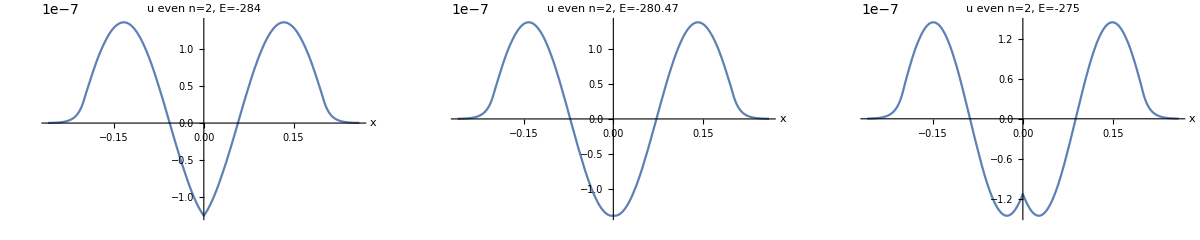

```mathematica
Do[    ex=eee[[i]];

wf2LeftE =NDSolve[ {  shrEq[ex,x]@f2Left[x],f2Left[-L]==u1[ex,-L],f2Left'[-L] ==g[ex]*Exp[-g[ex]*L] },f2Left[x], {x, -L,0} ]//Flatten;
wf2Left[x_]=f2Left[x]/.wf2LeftE;

wf2REvenE=NDSolve[ {  shrEq[ex,x]@f2REven[x],f2REven[L]==u3Even[ex,L],f2REven'[L] ==-g[ex]*Exp[-g[ex]*L] },
 f2REven[x], {x,0,L} ]//Flatten;
wf2REven[x_]=f2REven[x]/.wf2REvenE;

fig[[i]] = Plot[  Evaluate[wfEven[ex,wf2Left[x],wf2REven[x] ]] , {x, -1.3*L,1.3*L},  PlotRange->All,
AxesLabel->{"x", "     u even n=2,"StringForm[ "E=``",eee[[i]]," "]  }   
 ],
 {i,1,3} ]
fig123= GraphicsGrid[{{fig[[1]],fig[[2]],fig[[3]] } } ]
```

```mathematica
(* ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

```mathematica
(* ΕΠΙΛΥΣΗ ΤΗΣ ΕΞΙΣΩΣΗΣ SCHRODINGER ΓΙΑ ΤΙΣ 3 ΙΔΙΟΤΙΜΕΣ ΤΗΣ ΕΝΕΡΓΕΙΑΣ ΚΑΙ ΓΡΑΦΙΚΗ ΑΠΕΙΚΟΝΙΣΗ ΤΗΣ ΑΝΤΙΣΤΟΙΧΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ *)
```

```mathematica
Do[    ex=eee[[i]];

wf2LeftE =NDSolve[ {  shrEq[ex,x]@f2Left[x],f2Left[-L]==u1[ex,-L],f2Left'[-L] ==g[ex]*Exp[-g[ex]*L] },f2Left[x], {x, -L,0} ]//Flatten;
wf2Left[x_]=f2Left[x]/.wf2LeftE;

wf2ROddE=NDSolve[ {  shrEq[ex,x]@f2ROdd[x],f2ROdd[L]==u3Odd[ex,L],f2ROdd'[L] ==-g[ex]*Exp[-g[ex]*L] },
 f2ROdd[x], {x,0,L} ]//Flatten;
wf2ROdd[x_]=f2ROdd[x]/.wf2ROddE;

fig[[i]] = Plot[  Evaluate[wfOdd[ex,wf2Left[x],wf2ROdd[x] ]] , {x, -1.3*L,1.3*L},  PlotRange->All,
AxesLabel->{"x", "     u even n=2,"StringForm[ "E=``",eee[[i]]," "]  }   
 ],
 {i,1,3} ]
fig123= GraphicsGrid[{{fig[[1]],fig[[2]],fig[[3]] } } ]
```